# Proyecto

## Novoa Gastaldi Alejandro Silvestre

(silvestre.novoa@ciencias.unam.mx)

## ------ Sistema con deformación localizada tipo gaussiana y Dependiente de espín.

```mathematica
Clear["Global`*"]

s=-1;   (*Valor Cuantizado de Espín. +1 dara una solución y -1 dara la segunda*)
Rs=+1;   (*Parametro de las dos soluciones de RSOC. +1 dara una solución y -1 dara la segunda*)


Zigzag=10.;
Armchair=10.;

NZigzag=1.+2*Zigzag;
NArmchair=2*Armchair;

NEdos=1*NZigzag*NArmchair;

ε=0;  (*Energía de Sitio*)
εz=0;  (*Valor de Splitting Zeeman de la Energía de Sitio. Causado por un potencial externo. Dependiente del Espín.*)
εAB=0.0;  (*Valor de Splitting de la Energía de Sitio. Causado por un potencial externo. Dependiente de la Subred*)
t=1;  (*Energía de Transición (Tuneleo)*)



(*******Intrinseco*******)
λI=0.01;
tλI=(ⅈ/(3*Sqrt[3]))*λI*s;

(*******Valley-Zeeman*******)
λVZ=0.01;
tλVZ=(ⅈ/(3*Sqrt[3]))*λVZ*s;

(*******RSOC*******)
λR=0.01;
tλR=(2*ⅈ/3)*λR*s;








a=0.000000000142;   (*Distancia entre átomos*)
b=0.000000000246; (*Distancia entre hexagonos de Grafeno por el lado zig zag*)


epsi=0.;  (*Constante de deformación*)
theta=0;   (*Angulo respecto a la deformacion*)
young=0.165;  (*Modulo de Young del Grafeno*)
def=epsi*{{Cos[theta]^2-young*Sin[theta]^2,(1+young)*Cos[theta]*Sin[theta]},{(1+young)*Cos[theta]*Sin[theta],Sin[theta]^2-young*Cos[theta]^2}}; (*Tensor sociado a la deformación lineal*)


(*Vectores posición originales a primeros vecinos*)
dist10={0,b/Sqrt[3]};
dist20=(b/2)*{1,-1/Sqrt[3]};
dist30=(b/2)*{-1,-1/Sqrt[3]}; (*Los vectores fueron asignados considerando el zigzag en la dirección x*)

(*Vectores posición Deformados*)
dist1=({{1,0},{0,1}}+def).dist10;
dist2=({{1,0},{0,1}}+def).dist20;
dist3=({{1,0},{0,1}}+def).dist30;







(*Energías de Transición asociadas a la deformación y dirección de k*)


t1=t*Exp[-3.37*(Sqrt[3]*Norm[dist1]/b-1)];
t2=t*Exp[-3.37*(Sqrt[3]*Norm[dist2]/b-1)];
t3=t*Exp[-3.37*(Sqrt[3]*Norm[dist3]/b-1)];






(*Deformación Gaussiana*)
(*Se define la parametrización*)
Ampl=3*0.000000000142;  (*Amplitud de la deformación*)
Bvarx=0.5*0.000000000492;  (*Varianza en dirección x*)
Bvary=0.5*0.000000000492;   (*Varianza en dirección y*)
Largo=2*a*NArmchair/2-a;
Ancho=Sqrt[3]*a*(NZigzag-1)/2;
Xo=6*a+Largo/2;   (*Se define el centro de la deformación centrosimetrica*)
Yo=Ancho/2;    (*Es el centro de la banda pero este puede ser desplazado*)
gauss[x_,y_]:=Ampl*Exp[-((x-Xo)/Bvarx)^2 -((y-Yo)/Bvary)^2 ];    (*Función Gaussiana*)
Largo
Ancho
Plot3D[gauss[x,y],{x,0,Largo},{y,0,Ancho}]
```

2.698×10^-9

2.45951×10^-9

-Graphics3D-

(1)
 |  |  |  |

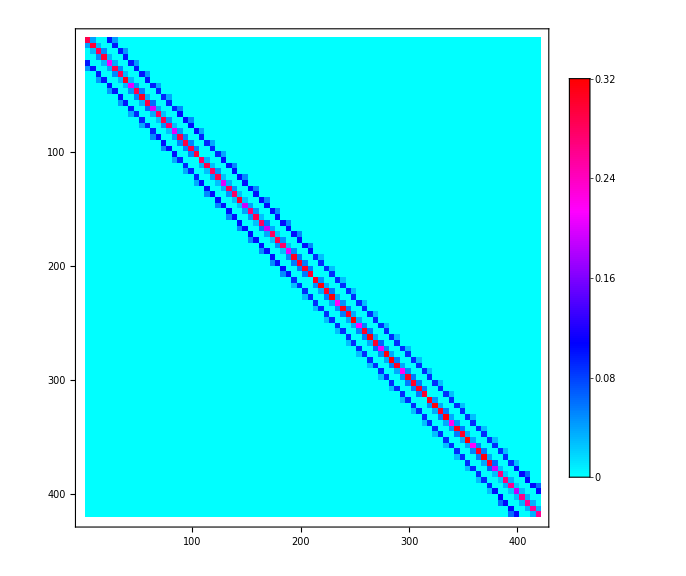

```mathematica
(*Se definiran las posiciones de los átomos de la red, centrando una esquina los ejes*)
PosAux1=Table[If[OddQ[i],{a/2,(Mod[i,NZigzag,1]-1)*a*Sqrt[3]/2},{0,(Mod[i,NZigzag,1]-1)*a*Sqrt[3]/2}],{i,1,NZigzag}];(*Pocisiones de primera columna*)
PosAux2=Table[{0,0},{i,1,2*NZigzag}];  (*Matriz auxiliar para la segunda columna*)
Pos=Table[{0,0},{i,1,NEdos}];  (*Matriz auxiliar para toda la nanocinta*)

Do[PosAux2[[i]]=PosAux1[[Mod[i,NZigzag,1]]],{i,1,2*NZigzag}];
Do[PosAux2[[i,1]]=PosAux2[[i,1]]+a*Mod[i-1,2,1],{i,NZigzag+1,2*NZigzag}];  (*Se asignan las posiciones de la segunda columna*)

Do[Pos[[i]]=PosAux2[[Mod[i,2*NZigzag,1]]],{i,1,NEdos}];
Do[Pos[[i,1]]=Pos[[i,1]]+3*a*IntegerPart[(i-1)/(2*NZigzag)],{i,2*NZigzag+1,NEdos}];  (*Se asignan las posiciones de todos los atomos en la red*)


PosDef=Table[{Pos[[i,1]],Pos[[i,2]],gauss[Pos[[i,1]],Pos[[i,2]]]},{i,1,NEdos}];  (*Se definen las nuevas posiciones debido a la deformación*)

(*Se dan los parametros de traslape de la primer diagonal que consideran de la deformación*)
tDef21=Table[{t*Exp[-3.37*(Norm[PosDef[[i]]-PosDef[[i+1]]]/a-1)]},{i,1,NEdos-1}]; 
Do[tDef21[[NZigzag*i]]={0},{i,1,NArmchair-1}];

(*Se dan los parametros de traslape entre columnas que consideran de la deformación*)
tDefm1=Table[{t*Exp[-3.37*(Norm[PosDef[[i]]-PosDef[[i+NZigzag]]]/a-1)]},{i,1,NEdos-NZigzag}]; 
Do[tDefm1[[2*i]]={0},{i,1,(NEdos-NZigzag)/2}];




H1=SparseArray[{{i_,i_}-> ε+s*εz},{NEdos,NEdos}]; (*Diagonal: Energías de Sitio*)
Do[H1[[i+1,i]]=tDef21[[i,1]]+Rs*tλR,{i,1,NEdos-1}];  (*Primera Diagonal Superior*)
Do[H1[[i+NZigzag,i]]=tDefm1[[i,1]]+Rs*tλR,{i,1,NEdos-NZigzag}];  (*Diagonal Superior de interacción entre columnas*)

(*Hamiltoniano de interacciones del grafeno*)
HEdoBase=H1+ConjugateTranspose[H1];


H2=SparseArray[{Band[{1,1}]->0.},{NEdos,NEdos}];
Do[H2[[i+1,i]]=tλI,{i,1,NEdos-1}];  (*Primera Diagonal Superior*)
Do[H2[[i+NZigzag,i]]=tλI,{i,1,NEdos-NZigzag}];  (*Diagonal Superior de interacción entre columnas*)
HEdoBase=HEdoBase+H2-ConjugateTranspose[H2];

HEdoBase // MatrixForm
MatrixPlot[ Re[HEdoBase] ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]
```

```mathematica
(********************* ----- HAMILTONIANO en Espacio Real ----- *********************)

(*Para este problema simplificado queda identico*)

HReal = HEdoBase ;
HEdoBase // MatrixForm;
MatrixPlot[HEdoBase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]


(* Para usar Green se requiere el Hamiltoniano discretiado (Matriz) en el espacio Real *)


(* Con Green obtendremos observables en función de la energía *)
Energia=En*IdentityMatrix[   Round[NEdos]    ];


(* Se ingresa las posiciones atomicas que actuaran de Fuente y Drenante *)
PosicionFuente=Table[   i   ,{i,1,NZigzag,1}];     (*Table[   i   ,{i,1,NZigzag,1}]*)
PosicionDrentante=Table[   NEdos-NZigzag+i   ,{i,1,NZigzag,1}];

PosicionFuente=  Table   [    Round[{PosicionFuente[[i]] , PosicionFuente[[i]] }]    ,{i,1, Length[PosicionFuente],1}];              (* Genera las posiciones correspondientes a la matriz *)
PosicionDrentante=  Table   [    Round[{PosicionDrentante[[i]] , PosicionDrentante[[i]] }]    ,{i,1, Length[PosicionDrentante],1}];

(* Matrices de Autoenergías *)
SigmaFuente=-ⅈ *tF *SparseArray[{        PosicionFuente->Table[1. , {i,1, Length[PosicionFuente],1} ]        },{NEdos,NEdos}];
SigmaDrenante= -ⅈ*tD*SparseArray[{        PosicionDrentante->Table[1. , {i,1, Length[PosicionDrentante],1} ]        },{NEdos,NEdos}];


tF=1.;
tD=1.;
t1=1.;
```

-Graphics-

```mathematica
(********************* ----- I Operador ----- *********************)

(*
(*  Solución Numerica   *)
{eval,evec}=Eigensystem[HEdoBase,  1,Method->{"Arnoldi","Criteria"->"RealPart"} ]

Print[     Style["Energias Numericas ",18,Bold,Purple]      ]
Style[    MatrixForm[  eval  ]   ,{Medium,Bold,Purple}]



(*  Solución Exacta:    Usa el mismo hamiltoniano de interacción   *)

t1*HEdoBase   // MatrixForm;

Print[     Style["Energias Exactas ",18,Bold,Purple]      ]
Quiet[        Solve[   Det[           t1*HEdoBase-En*IdentityMatrix[   Round[NEdos]    ]          ]==0    ,En]          ]

(*Eigenfunction*)







eval[[1]];
EdoBase=evec[[1]];


(*    Subscript[I, i] = ⅈ*(e/h)*2*π*( H Gn - Gn H )         Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)
(HEdoBase- SigmaFuente  -  SigmaDrenante) *GnMatrizDensidad // MatrixForm;

GnMatrizDensidad=Table[    Table[   Conjugate[  EdoBase[[ j ]]  ]*EdoBase[[ i ]]   ,{i,1,NEdos,1}]   ,{j,1,NEdos,1}];
GnMatrizDensidad // MatrixForm;

IOperador=ⅈ*(   ( HEdoBase    +  SigmaDrenante) *GnMatrizDensidad   +   GnMatrizDensidad   * ( HEdoBase  +  SigmaDrenante)   ) ;

IVal=Im[IOperador];
IVal// MatrixForm





ILocalY=Table[         Table[     -IVal[[il,  (jl-1)*NZigzag+Mod[il-1,NZigzag,1]  ]]+ IVal[[il, (jl-1)*NZigzag+Mod[il+1,NZigzag,1]   ]]     , {il, 1+(jl-1)*NZigzag,jl*NZigzag,1}]    , {jl,1,NArmchair,1}];
ILocalY=Flatten[ ILocalY];

ILocalX=   Join[     Table[    IVal[[il,il+NZigzag ]]     ,{il,1,NZigzag*(NArmchair-1),1}  ] , Table[ 0., {jl,1,NZigzag,1}]      ];



ILocal=              Table[  {       {  1.+IntegerPart[   (i-1)/(NZigzag ) ],  Mod[ i,NZigzag,1.]     }   ,       {ILocalX[[i]],  ILocalY[[i]] }    } ,   {i,1, NEdos,1.}];     


ListVectorPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow",VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]
ListStreamPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow", VectorPoints->10, VectorScale->0.08, PlotLegends->Automatic]


Clear[En]


(*    Subscript[J, i] = 2*J*( Subscript[b, i+1]^† Subscript[b, i] - Subscript[b, i-1]^† Subscript[b, i])         Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)

*)
```

```mathematica
(* Con Green obtendremos observables en función de la energía *)
EnMin=-4.;
EnMax=4.;
NEnPuntos=501.;

DEn = Abs[EnMax-EnMin]/ (NEnPuntos-1.);
EnergiasValores=Table [   ( i )      ,{i,EnMin,EnMax,DEn}     ];


Energia=    Table [   ( i )*IdentityMatrix[   Round[NEdos]    ]       ,{i,EnMin,EnMax,DEn}     ];





(*Broadening Matrix*)
GammaFuente = ⅈ*(  SigmaFuente -ConjugateTranspose[  SigmaFuente ]);
GammaDrenante= ⅈ*(  SigmaDrenante -ConjugateTranspose[  SigmaDrenante ]);





(*Funcion de Green del Nanosistema*)
FGreen= Table[        Inverse[  Energia [[i]]  -  HEdoBase  - SigmaFuente  -  SigmaDrenante   ]       , {i,1,NEnPuntos,1}];
```

Función de Transmisión

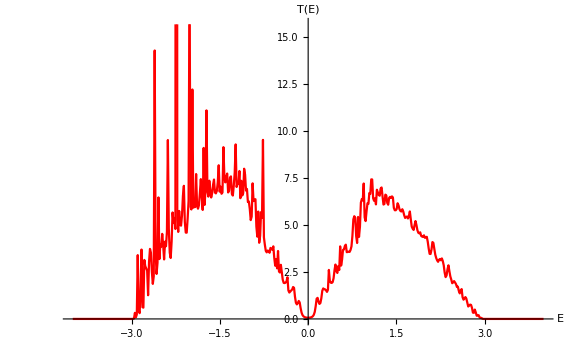

DOS

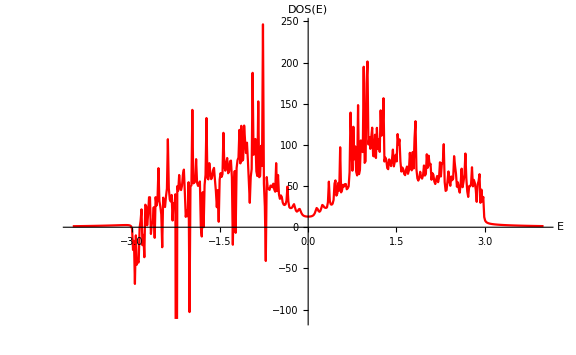

LDOS

-Graphics-

```mathematica
(*Funcion de Transmision*)
Print[     Style["Función de Transmisión",18,Bold,Purple]      ]
FTranmision= Table[          { EnMin  +  DEn*(i-1)   ,      Tr[     GammaDrenante.  FGreen[[i]]  .GammaFuente.ConjugateTranspose[   FGreen[[i]]  ]     ]  }      , {i,1,NEnPuntos,1}];

ListPlot[     FTranmision    ,PlotStyle->{{PointSize[0.01],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"T(E)"}, ImageSize->Large,   Joined->True]






(*Función Espectral*)
A=   Table[         ⅈ*(  FGreen[[i]]  -  ConjugateTranspose[  FGreen[[i]]  ]  )       , {i,1,NEnPuntos,1}];



(*DOS: Densidad de Estados*)
Print[     Style["DOS",18,Bold,Purple]      ]
DOS=    Table[        { EnMin  +  DEn*(i-1)   ,       Re[   Tr[  A[[i]]  ]/(2*π)   ]   }     , {i,1,NEnPuntos,1}];

ListPlot[     DOS    ,PlotStyle->{{PointSize[0.01],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"DOS(E)"}, ImageSize->Large,   Joined->True]


(*LDOS: Densidad Local de Estados*)
Print[     Style["LDOS",18,Bold,Purple]      ]
LDOS=    Table[              Re[  Diagonal[  A[[i]]   ]/(2*π)  ]           , {i,1,NEnPuntos,1}];     (*Los elementos de la Diagonal de A *)

LDOSSitios=Table[                   Table[         { EnMin  +  DEn*(i-1)   ,         LDOS[[i,j]]   }       ,     {i,1,NEnPuntos,1}]                   ,     {j,1,NEdos,1}] ;
ListPlot[     LDOSSitios     ,PlotStyle->{{PointSize[0.012],Blue},{PointSize[0.015],Red},{PointSize[0.01],Green},{PointSize[0.006],Orange},{PointSize[0.003],Yellow},{PointSize[0.008],Pink}},LabelStyle->{14,Black},AxesLabel->{"E" ,"LDOS(E)"}, ImageSize->Large,   Joined->True]
```

```mathematica
EnergiasValores
```

{-4.,-3.984,-3.968,-3.952,-3.936,-3.92,-3.904,-3.888,-3.872,-3.856,-3.84,-3.824,-3.808,-3.792,-3.776,-3.76,-3.744,-3.728,-3.712,-3.696,-3.68,-3.664,-3.648,-3.632,-3.616,-3.6,-3.584,-3.568,-3.552,-3.536,-3.52,-3.504,-3.488,-3.472,-3.456,-3.44,-3.424,-3.408,-3.392,-3.376,-3.36,-3.344,-3.328,-3.312,-3.296,-3.28,-3.264,-3.248,-3.232,-3.216,-3.2,-3.184,-3.168,-3.152,-3.136,-3.12,-3.104,-3.088,-3.072,-3.056,-3.04,-3.024,-3.008,-2.992,-2.976,-2.96,-2.944,-2.928,-2.912,-2.896,-2.88,-2.864,-2.848,-2.832,-2.816,-2.8,-2.784,-2.768,-2.752,-2.736,-2.72,-2.704,-2.688,-2.672,-2.656,-2.64,-2.624,-2.608,-2.592,-2.576,-2.56,-2.544,-2.528,-2.512,-2.496,-2.48,-2.464,-2.448,-2.432,-2.416,-2.4,-2.384,-2.368,-2.352,-2.336,-2.32,-2.304,-2.288,-2.272,-2.256,-2.24,-2.224,-2.208,-2.192,-2.176,-2.16,-2.144,-2.128,-2.112,-2.096,-2.08,-2.064,-2.048,-2.032,-2.016,-2.,-1.984,-1.968,-1.952,-1.936,-1.92,-1.904,-1.888,-1.872,-1.856,-1.84,-1.824,-1.808,-1.792,-1.776,-1.76,-1.744,-1.728,-1.712,-1.696,-1.68,-1.664,-1.648,-1.632,-1.616,-1.6,-1.584,-1.568,-1.552,-1.536,-1.52,-1.504,-1.488,-1.472,-1.456,-1.44,-1.424,-1.408,-1.392,-1.376,-1.36,-1.344,-1.328,-1.312,-1.296,-1.28,-1.264,-1.248,-1.232,-1.216,-1.2,-1.184,-1.168,-1.152,-1.136,-1.12,-1.104,-1.088,-1.072,-1.056,-1.04,-1.024,-1.008,-0.992,-0.976,-0.96,-0.944,-0.928,-0.912,-0.896,-0.88,-0.864,-0.848,-0.832,-0.816,-0.8,-0.784,-0.768,-0.752,-0.736,-0.72,-0.704,-0.688,-0.672,-0.656,-0.64,-0.624,-0.608,-0.592,-0.576,-0.56,-0.544,-0.528,-0.512,-0.496,-0.48,-0.464,-0.448,-0.432,-0.416,-0.4,-0.384,-0.368,-0.352,-0.336,-0.32,-0.304,-0.288,-0.272,-0.256,-0.24,-0.224,-0.208,-0.192,-0.176,-0.16,-0.144,-0.128,-0.112,-0.096,-0.08,-0.064,-0.048,-0.032,-0.016,0.,0.016,0.032,0.048,0.064,0.08,0.096,0.112,0.128,0.144,0.16,0.176,0.192,0.208,0.224,0.24,0.256,0.272,0.288,0.304,0.32,0.336,0.352,0.368,0.384,0.4,0.416,0.432,0.448,0.464,0.48,0.496,0.512,0.528,0.544,0.56,0.576,0.592,0.608,0.624,0.64,0.656,0.672,0.688,0.704,0.72,0.736,0.752,0.768,0.784,0.8,0.816,0.832,0.848,0.864,0.88,0.896,0.912,0.928,0.944,0.96,0.976,0.992,1.008,1.024,1.04,1.056,1.072,1.088,1.104,1.12,1.136,1.152,1.168,1.184,1.2,1.216,1.232,1.248,1.264,1.28,1.296,1.312,1.328,1.344,1.36,1.376,1.392,1.408,1.424,1.44,1.456,1.472,1.488,1.504,1.52,1.536,1.552,1.568,1.584,1.6,1.616,1.632,1.648,1.664,1.68,1.696,1.712,1.728,1.744,1.76,1.776,1.792,1.808,1.824,1.84,1.856,1.872,1.888,1.904,1.92,1.936,1.952,1.968,1.984,2.,2.016,2.032,2.048,2.064,2.08,2.096,2.112,2.128,2.144,2.16,2.176,2.192,2.208,2.224,2.24,2.256,2.272,2.288,2.304,2.32,2.336,2.352,2.368,2.384,2.4,2.416,2.432,2.448,2.464,2.48,2.496,2.512,2.528,2.544,2.56,2.576,2.592,2.608,2.624,2.64,2.656,2.672,2.688,2.704,2.72,2.736,2.752,2.768,2.784,2.8,2.816,2.832,2.848,2.864,2.88,2.896,2.912,2.928,2.944,2.96,2.976,2.992,3.008,3.024,3.04,3.056,3.072,3.088,3.104,3.12,3.136,3.152,3.168,3.184,3.2,3.216,3.232,3.248,3.264,3.28,3.296,3.312,3.328,3.344,3.36,3.376,3.392,3.408,3.424,3.44,3.456,3.472,3.488,3.504,3.52,3.536,3.552,3.568,3.584,3.6,3.616,3.632,3.648,3.664,3.68,3.696,3.712,3.728,3.744,3.76,3.776,3.792,3.808,3.824,3.84,3.856,3.872,3.888,3.904,3.92,3.936,3.952,3.968,3.984,4.}

LDOS

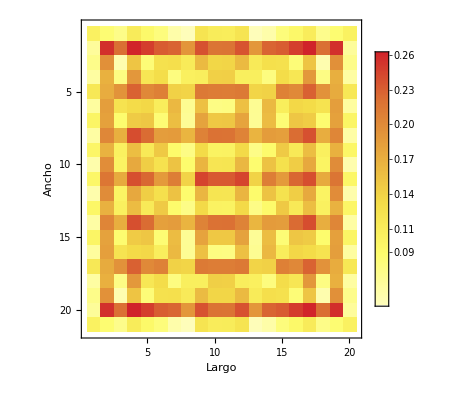

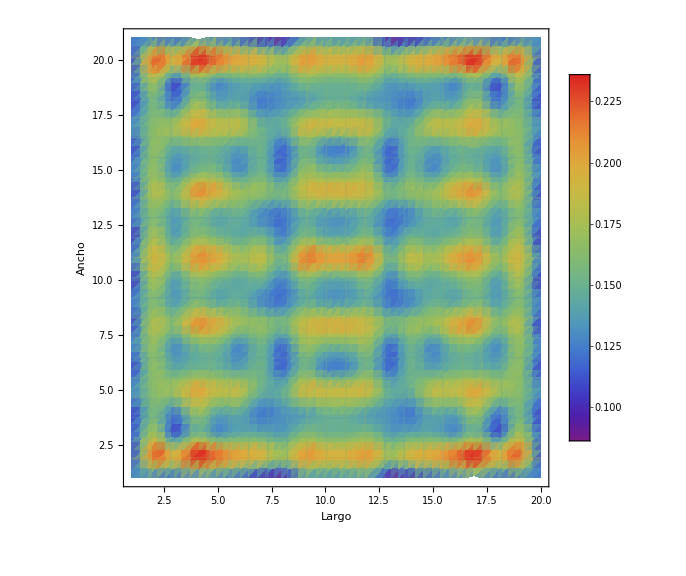

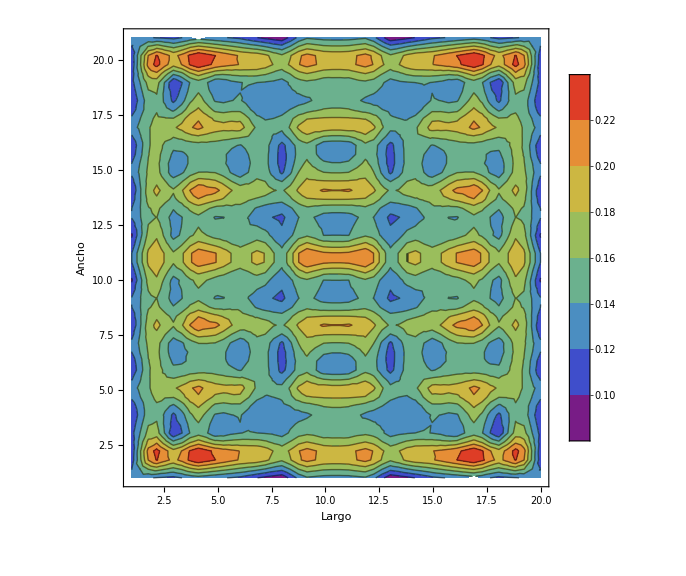

```mathematica
(*LDOS en Espacio REAL*)
Print[     Style["LDOS",18,Bold,Purple]      ]
EnVal=2;
NEn=1.+ ( EnVal-EnMin ) /DEn; 


LDOSRealMatrix=     Table[              SparseArray[  {{i_,i_}->0.},{NZigzag,NArmchair}  ]            , {j,1,NEnPuntos,1}];
Do[         Do[       LDOSRealMatrix [[j,       Mod[ i,NZigzag,1.]  ,   1.+IntegerPart[   (i-1)/NZigzag  ]   ]]=Re[  LDOS [[j,i]]  ]      ,   {i,1,NEdos,1.}]            , {j,1,NEnPuntos,1}];

MatrixPlot[     LDOSRealMatrix [[NEn]]   ,PlotTheme->"Detailed",ColorFunction->"TemperatureMap",FrameLabel->{{"Largo",HoldForm["=E  "]En},{"Ancho",None}}]


LDOSRealDensity=     Table[              Table[  {  1.+IntegerPart[   (i-1)/NZigzag  ],  Mod[ i,NZigzag,1.],    Re[  LDOS [[j,i]]  ]} ,   {i,1,NEdos,1.}]           , {j,1,NEnPuntos,1}];

ListDensityPlot[     LDOSRealDensity [[NEn]]      ,FrameLabel->{{"Ancho",StringTemplate["E = `1` t"][En]},{"Largo",None}}, ImageSize->Large,ColorFunction->"Rainbow",InterpolationOrder->1, MaxPlotPoints->50, Mesh->{20,21},PlotLegends->Automatic]
ListContourPlot[     LDOSRealDensity [[NEn]]      ,FrameLabel->{{"Ancho",StringTemplate["E = `1` t"][En]},{"Largo",None}}, ImageSize->Large,ColorFunction->"Rainbow",InterpolationOrder->1, MaxPlotPoints->50, Mesh->{6,7},PlotLegends->Automatic]
```

```mathematica
(********** -------- Corriente -------- **********)
Print[     Style["Corriente Total",18,Bold,Purple]      ]
fFermi2=1;           (*Suponiendo Funciones de Fermi iguales a 1*)
SigmaDispersiva=GammaFuente;         (*Energías de Dispersión, In-Scattering*)
FGreenIn=     Table[               FGreen[[i]] .  SigmaDispersiva.  ConjugateTranspose[   FGreen[[i]]  ]            , {i,1,NEnPuntos,1}];         (*Funcion de Green de Dispersión*)
IVal=    Table[              Im[  2*FGreenIn[[i]]*fFermi2  ]            , {i,1,NEnPuntos,1}];          (*Matrices con los valores de las corrientes*)
ITotal=    Table[           { EnMin  +  DEn*(i-1)   ,         Tr[  IVal[[i]]  ]      }          , {i,1,NEnPuntos,1}];      (*Corriente Total en Función de la Energía: Unidades (h/e)*)


ListPlot[       ITotal     ,PlotStyle->{{PointSize[0.0065],Red}},LabelStyle->{14,Black},AxesLabel->{"E" ,"I [h/e]"}, ImageSize->Large]
```

Corriente Total

```mathematica
EnergiasValores
```

{-4.,-3.984,-3.968,-3.952,-3.936,-3.92,-3.904,-3.888,-3.872,-3.856,-3.84,-3.824,-3.808,-3.792,-3.776,-3.76,-3.744,-3.728,-3.712,-3.696,-3.68,-3.664,-3.648,-3.632,-3.616,-3.6,-3.584,-3.568,-3.552,-3.536,-3.52,-3.504,-3.488,-3.472,-3.456,-3.44,-3.424,-3.408,-3.392,-3.376,-3.36,-3.344,-3.328,-3.312,-3.296,-3.28,-3.264,-3.248,-3.232,-3.216,-3.2,-3.184,-3.168,-3.152,-3.136,-3.12,-3.104,-3.088,-3.072,-3.056,-3.04,-3.024,-3.008,-2.992,-2.976,-2.96,-2.944,-2.928,-2.912,-2.896,-2.88,-2.864,-2.848,-2.832,-2.816,-2.8,-2.784,-2.768,-2.752,-2.736,-2.72,-2.704,-2.688,-2.672,-2.656,-2.64,-2.624,-2.608,-2.592,-2.576,-2.56,-2.544,-2.528,-2.512,-2.496,-2.48,-2.464,-2.448,-2.432,-2.416,-2.4,-2.384,-2.368,-2.352,-2.336,-2.32,-2.304,-2.288,-2.272,-2.256,-2.24,-2.224,-2.208,-2.192,-2.176,-2.16,-2.144,-2.128,-2.112,-2.096,-2.08,-2.064,-2.048,-2.032,-2.016,-2.,-1.984,-1.968,-1.952,-1.936,-1.92,-1.904,-1.888,-1.872,-1.856,-1.84,-1.824,-1.808,-1.792,-1.776,-1.76,-1.744,-1.728,-1.712,-1.696,-1.68,-1.664,-1.648,-1.632,-1.616,-1.6,-1.584,-1.568,-1.552,-1.536,-1.52,-1.504,-1.488,-1.472,-1.456,-1.44,-1.424,-1.408,-1.392,-1.376,-1.36,-1.344,-1.328,-1.312,-1.296,-1.28,-1.264,-1.248,-1.232,-1.216,-1.2,-1.184,-1.168,-1.152,-1.136,-1.12,-1.104,-1.088,-1.072,-1.056,-1.04,-1.024,-1.008,-0.992,-0.976,-0.96,-0.944,-0.928,-0.912,-0.896,-0.88,-0.864,-0.848,-0.832,-0.816,-0.8,-0.784,-0.768,-0.752,-0.736,-0.72,-0.704,-0.688,-0.672,-0.656,-0.64,-0.624,-0.608,-0.592,-0.576,-0.56,-0.544,-0.528,-0.512,-0.496,-0.48,-0.464,-0.448,-0.432,-0.416,-0.4,-0.384,-0.368,-0.352,-0.336,-0.32,-0.304,-0.288,-0.272,-0.256,-0.24,-0.224,-0.208,-0.192,-0.176,-0.16,-0.144,-0.128,-0.112,-0.096,-0.08,-0.064,-0.048,-0.032,-0.016,0.,0.016,0.032,0.048,0.064,0.08,0.096,0.112,0.128,0.144,0.16,0.176,0.192,0.208,0.224,0.24,0.256,0.272,0.288,0.304,0.32,0.336,0.352,0.368,0.384,0.4,0.416,0.432,0.448,0.464,0.48,0.496,0.512,0.528,0.544,0.56,0.576,0.592,0.608,0.624,0.64,0.656,0.672,0.688,0.704,0.72,0.736,0.752,0.768,0.784,0.8,0.816,0.832,0.848,0.864,0.88,0.896,0.912,0.928,0.944,0.96,0.976,0.992,1.008,1.024,1.04,1.056,1.072,1.088,1.104,1.12,1.136,1.152,1.168,1.184,1.2,1.216,1.232,1.248,1.264,1.28,1.296,1.312,1.328,1.344,1.36,1.376,1.392,1.408,1.424,1.44,1.456,1.472,1.488,1.504,1.52,1.536,1.552,1.568,1.584,1.6,1.616,1.632,1.648,1.664,1.68,1.696,1.712,1.728,1.744,1.76,1.776,1.792,1.808,1.824,1.84,1.856,1.872,1.888,1.904,1.92,1.936,1.952,1.968,1.984,2.,2.016,2.032,2.048,2.064,2.08,2.096,2.112,2.128,2.144,2.16,2.176,2.192,2.208,2.224,2.24,2.256,2.272,2.288,2.304,2.32,2.336,2.352,2.368,2.384,2.4,2.416,2.432,2.448,2.464,2.48,2.496,2.512,2.528,2.544,2.56,2.576,2.592,2.608,2.624,2.64,2.656,2.672,2.688,2.704,2.72,2.736,2.752,2.768,2.784,2.8,2.816,2.832,2.848,2.864,2.88,2.896,2.912,2.928,2.944,2.96,2.976,2.992,3.008,3.024,3.04,3.056,3.072,3.088,3.104,3.12,3.136,3.152,3.168,3.184,3.2,3.216,3.232,3.248,3.264,3.28,3.296,3.312,3.328,3.344,3.36,3.376,3.392,3.408,3.424,3.44,3.456,3.472,3.488,3.504,3.52,3.536,3.552,3.568,3.584,3.6,3.616,3.632,3.648,3.664,3.68,3.696,3.712,3.728,3.744,3.76,3.776,3.792,3.808,3.824,3.84,3.856,3.872,3.888,3.904,3.92,3.936,3.952,3.968,3.984,4.}

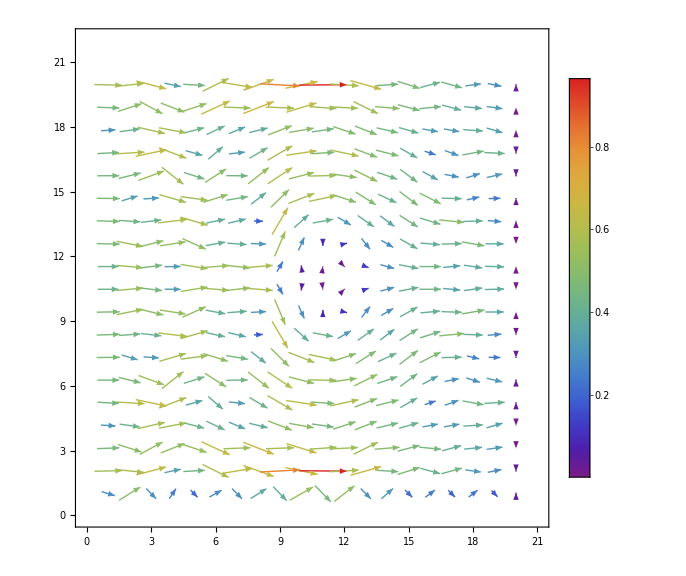

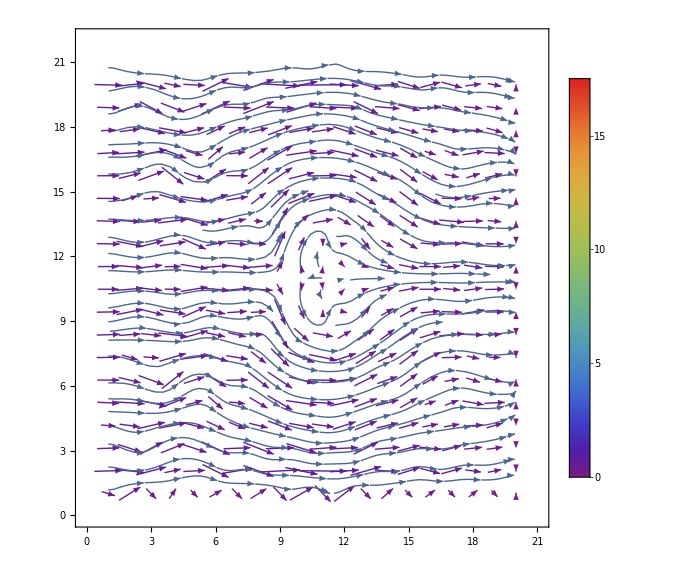

```mathematica
(*Corriente LOCAL*)
EnVal=2;
NEn=1.+ ( EnVal-EnMin ) /DEn; 

IVal[[  NEn  ]] // MatrixForm;


ILocalY=Table[         Table[     -IVal[[NEn,il,  (jl-1)*NZigzag+Mod[il-1,NZigzag,1]  ]]+ IVal[[NEn,il, (jl-1)*NZigzag+Mod[il+1,NZigzag,1]   ]]     , {il, 1+(jl-1)*NZigzag,jl*NZigzag,1}]    , {jl,1,NArmchair,1}];
ILocalY=Flatten[ ILocalY];

ILocalX=   Join[     Table[    IVal[[NEn,il,il+NZigzag ]]     ,{il,1,NZigzag*(NArmchair-1),1}  ] , Table[ 0., {jl,1,NZigzag,1}]      ];



ILocal=              Table[  {       {  1.+IntegerPart[   (i-1)/(NZigzag ) ],  Mod[ i,NZigzag,1.]     }   ,       {ILocalX[[i]],  ILocalY[[i]] }    } ,   {i,1, NEdos,1.}];     


ListVectorPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow",VectorPoints->20, VectorScale->0.08, PlotLegends->Automatic]
ListStreamPlot[      ILocal     ,ImageSize->Large, VectorColorFunction->"Rainbow", VectorPoints->20, VectorScale->0.08, PlotLegends->Automatic]
```